# Adaptive dynamics of sexual selection in a stratified human society

- Intra-sexual competition: competition between males = dominance for access to higher social classes, and thus
	-> food resources of higher quality
	-> more mates

- Inter-sexual selection: selection of females on attractivity = honest cue of fertility, by males of higher choosiness. Choosiness negatively affects a male’s mating rate, but a more choosy male mates with more fertile females.

- Adaptation to the “local” environment: population initially adapted to high quality food (cf hunter-gatherers diet before stratification), but with stratification, people of the higher classes monopolize resources, leaving the lower classes with a poor diet that negatively affects survival. Can a mutation that allow for a better assimilation of low quality food, invade lower classes, as well as higher classes later on due to up-migration?

## 1. Dynamics of a system with no social classes

Reminder: always assume that the resident is at its demographic attractor, and as a consequence selection_resident(resident)=0 for all resident as otherwise the population would grow indefinitely

## Population growth

```mathematica
Clear[u, um, uf]
```

```mathematica
u[_time] := um[_time] + uf[_time]
```

```mathematica
um[_t] := um_resident[_t] + um_mutant[_t]
```

```mathematica
uf[_t] := uf_resident[_t] + uf_mutant[_t]
```

```mathematica
um_resident'[_time] := um_resident[_t]*(d0-deathRate[_t])
```

```mathematica
um_mutant'[_time] := um_mutant[_t]*(d1-deathRate[_t])
```

```mathematica
uf_resident'[_time] := uf_resident[_t]*(f0-deathRate[_t])
```

```mathematica
uf_mutant'[_time] := uf_mutant[_t]*(f1-deathRate[_t])
```

## Male mating success

```mathematica
Relative mating rate (alpha) of males d1 (dominant) versus d0 (resident)
```

```mathematica
alpha is a function of deltaMu, the differential in mating rate acquired with dominance mutation : mu_d0 = 1, mu_d1 = 1 + deltaMu
```

```mathematica
f[deltaMu_] := (1+deltaMu)/(2+deltaMu)
```

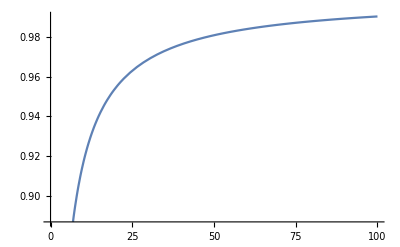

```mathematica
Plot[f[deltaMu],{deltaMu,0,100}]
```

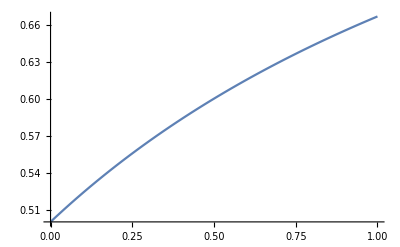

```mathematica
Plot[f[deltaMu],{deltaMu,0,1}]
```

```mathematica
Per-capita number of matings Q
```

```mathematica
Males of type 0 (resident) and 1 (dominant) both have the possibility of mating with females of type 0 (resident) or 1 (attractive) with proportion phi (choosiness).
NB : uXXX is the absolute population size of class XXX.
```

```mathematica
u :={uf0,uf1,um0,um1}
uf := uf0+uf1
um := um0+um1
```

```mathematica
Q0:= Q00+Q01
```

```mathematica
Q1:= Q10+Q11
```

```mathematica
Q00:= (1-phi)*(1-alpha)*uf0/um0
```

```mathematica
Q01:= phi*(1-alpha)*uf1/um0
```

```mathematica
Q10:= alpha*(1-phi)*uf0/um1
```

```mathematica
Q11:= alpha*phi*uf1/um0
```

```mathematica
Q0
Q1
```

((1-alpha) (1-phi) uf0)/um0+((1-alpha) phi uf1)/um0

(alpha phi uf1)/um0+(alpha (1-phi) uf0)/um1

## Selection gradients

```mathematica
DiffDelta:= W'[delta] + betaADelta*W'[a]+betaPhiDelta*W'[phi]+betaEtaDelta*W'[eta]
```

```mathematica
DiffA := W'[a]+betaADelta*W'[delta]+betaPhiA*W'[phi]+betaAEta*W'[eta]
```

```mathematica
DiffPhi := W'[phi] + betaPhiDelta*W'[delta]+betaPhiA*W'[a]+betaEtaPhi*W'[eta]
```

```mathematica
DiffEta:= W'[eta]+betaEtaDelta*W'[delta]+betaAEta*W'[a]+betaEtaPhi*W'[phi]
```

```mathematica
Solve[DiffDelta == 0 && DiffA == 0 && DiffPhi ==0 && DiffEta == 0, {W'[a],W'[delta],W'[eta],W'[phi]}]
```

{{W'[a]→0,W'[delta]→0,W'[eta]→0,W'[phi]→0}}

Test with only two differential equations. The solution is right, but the necessary condition beta1*beta2 =! 1 is lacking in the results!!!

```mathematica
Solve[diffParX+beta1*diffParY == 0 && diffParY + beta2*diffParX ==0, {diffParX,diffParY}]
```

{{diffParX→0,diffParY→0}}

How about solving the equation system via the matrix form?

```mathematica
m={{1,beta1},{beta2,1}}
```

{{1,beta1},{beta2,1}}

```mathematica
m.{X,Y}=={0,0}
```

{X+beta1 Y,beta2 X+Y}=={0,0}

```mathematica
Solve[%,{X,Y}]
```

{{X→0,Y→0}}

Below, with the Mathematica function Reduce, the solution is provided with the necessary condition

```mathematica
Reduce[m.{X,Y}=={0,0},{X,Y}]
```

(beta2≠0&&beta1==1/beta2&&Y==-beta2 X)||(-1+beta1 beta2≠0&&X==0&&Y==0)

Weirdly enough, when requiring X and Y to be reals, more solutions appear!!!

```mathematica
Reduce[m.{X,Y}=={0,0},{X,Y}, Reals]
```

(beta1==0&&X==0&&Y==0)||(((beta1<0&&beta2==1/beta1)||(beta1>0&&beta2==1/beta1)||(((beta2<0&&(beta1<1/beta2||1/beta2<beta1<0||beta1>0))||(beta2==0&&(beta1<0||beta1>0))||(beta2>0&&(beta1<0||0<beta1<1/beta2||beta1>1/beta2)))&&X==0))&&Y==-X/beta1)

Now, let’s apply the matrix technique to our 4 differential equations

```mathematica
m4 = {{1, betaADelta,betaPhiDelta,betaEtaDelta},{betaADelta,1,betaPhiA,betaAEta},{betaPhiDelta,betaPhiA,1,betaEtaPhi},{betaEtaDelta,betaAEta,betaEtaPhi,1}}
```

{{1,betaADelta,betaPhiDelta,betaEtaDelta},{betaADelta,1,betaPhiA,betaAEta},{betaPhiDelta,betaPhiA,1,betaEtaPhi},{betaEtaDelta,betaAEta,betaEtaPhi,1}}

```mathematica
m4.{W, X, Y, Z} == {0,0,0,0}
```

{W+betaADelta X+betaPhiDelta Y+betaEtaDelta Z,betaADelta W+X+betaPhiA Y+betaAEta Z,betaPhiDelta W+betaPhiA X+Y+betaEtaPhi Z,betaEtaDelta W+betaAEta X+betaEtaPhi Y+Z}=={0,0,0,0}

```mathematica
Solve[m4.{W, X, Y, Z} == {0,0,0,0}, {W, X, Y, Z}]
```

{{W→0,X→0,Y→0,Z→0}}

```mathematica
Resolve[m4.{W, X, Y, Z} == {0,0,0,0}, {W, X, Y, Z}]
```

W+betaADelta X+betaPhiDelta Y+betaEtaDelta Z==0&&betaADelta W+X+betaPhiA Y+betaAEta Z==0&&betaPhiDelta W+betaPhiA X+Y+betaEtaPhi Z==0&&betaEtaDelta W+betaAEta X+betaEtaPhi Y+Z==0

There does not seem to be any necessary restriction / condition to apply for the solutions to be true.

## Transition matrix

```mathematica
A := {{(2ha+1)*f0*s,(2(1-ha)+1)*f1*s,3*q0*s,3*q1*s},{(2(1-ha)+1)*f0*s,(2ha+1)*f1*s,3*q0*s,3*q1*s},{3*f0*s,3*f1*s,(2hd+1)*q0*s,(2(1-hd)+1)*q1*s},{3*f0*s,3*f1*s,(2(1-hd)+1)*q0*s, (2hd+1)*q1*s}}
```

Trying to find the right and left eigenvectors u and v respectively, which correspond to reproductive rate and classes ratios.

```mathematica
Solve[A*u==Eigenvalues[A]*u,u]
```

{{uf0→0,uf1→0,um0→0,um1→0}}

-> Null vector!

```mathematica
Clear[lambda]
```

```mathematica
Eigenvalues[A]
```

{s Root[-80 f0 f1 q0 q1+160 f0 f1 ha q0 q1+160 f0 f1 hd q0 q1-320 f0 f1 ha hd q0 q1+(-28 f0 f1 q0+56 f0 f1 ha q0+16 f0 f1 hd q0-32 f0 f1 ha hd q0-28 f0 f1 q1+56 f0 f1 ha q1+16 f0 f1 hd q1-32 f0 f1 ha hd q1-28 f0 q0 q1-28 f1 q0 q1+16 f0 ha q0 q1+16 f1 ha q0 q1+56 f0 hd q0 q1+56 f1 hd q0 q1-32 f0 ha hd q0 q1-32 f1 ha hd q0 q1) #1+(-8 f0 f1+16 f0 f1 ha-8 f0 q0-8 f1 q0+2 f0 ha q0+2 f1 ha q0+2 f0 hd q0+2 f1 hd q0+4 f0 ha hd q0+4 f1 ha hd q0-8 f0 q1-8 f1 q1+2 f0 ha q1+2 f1 ha q1+2 f0 hd q1+2 f1 hd q1+4 f0 ha hd q1+4 f1 ha hd q1-8 q0 q1+16 hd q0 q1) #1^2+(-f0-f1-2 f0 ha-2 f1 ha-q0-2 hd q0-q1-2 hd q1) #1^3+#1^4&,1],s Root[-80 f0 f1 q0 q1+160 f0 f1 ha q0 q1+160 f0 f1 hd q0 q1-320 f0 f1 ha hd q0 q1+(-28 f0 f1 q0+56 f0 f1 ha q0+16 f0 f1 hd q0-32 f0 f1 ha hd q0-28 f0 f1 q1+56 f0 f1 ha q1+16 f0 f1 hd q1-32 f0 f1 ha hd q1-28 f0 q0 q1-28 f1 q0 q1+16 f0 ha q0 q1+16 f1 ha q0 q1+56 f0 hd q0 q1+56 f1 hd q0 q1-32 f0 ha hd q0 q1-32 f1 ha hd q0 q1) #1+(-8 f0 f1+16 f0 f1 ha-8 f0 q0-8 f1 q0+2 f0 ha q0+2 f1 ha q0+2 f0 hd q0+2 f1 hd q0+4 f0 ha hd q0+4 f1 ha hd q0-8 f0 q1-8 f1 q1+2 f0 ha q1+2 f1 ha q1+2 f0 hd q1+2 f1 hd q1+4 f0 ha hd q1+4 f1 ha hd q1-8 q0 q1+16 hd q0 q1) #1^2+(-f0-f1-2 f0 ha-2 f1 ha-q0-2 hd q0-q1-2 hd q1) #1^3+#1^4&,2],s Root[-80 f0 f1 q0 q1+160 f0 f1 ha q0 q1+160 f0 f1 hd q0 q1-320 f0 f1 ha hd q0 q1+(-28 f0 f1 q0+56 f0 f1 ha q0+16 f0 f1 hd q0-32 f0 f1 ha hd q0-28 f0 f1 q1+56 f0 f1 ha q1+16 f0 f1 hd q1-32 f0 f1 ha hd q1-28 f0 q0 q1-28 f1 q0 q1+16 f0 ha q0 q1+16 f1 ha q0 q1+56 f0 hd q0 q1+56 f1 hd q0 q1-32 f0 ha hd q0 q1-32 f1 ha hd q0 q1) #1+(-8 f0 f1+16 f0 f1 ha-8 f0 q0-8 f1 q0+2 f0 ha q0+2 f1 ha q0+2 f0 hd q0+2 f1 hd q0+4 f0 ha hd q0+4 f1 ha hd q0-8 f0 q1-8 f1 q1+2 f0 ha q1+2 f1 ha q1+2 f0 hd q1+2 f1 hd q1+4 f0 ha hd q1+4 f1 ha hd q1-8 q0 q1+16 hd q0 q1) #1^2+(-f0-f1-2 f0 ha-2 f1 ha-q0-2 hd q0-q1-2 hd q1) #1^3+#1^4&,3],s Root[-80 f0 f1 q0 q1+160 f0 f1 ha q0 q1+160 f0 f1 hd q0 q1-320 f0 f1 ha hd q0 q1+(-28 f0 f1 q0+56 f0 f1 ha q0+16 f0 f1 hd q0-32 f0 f1 ha hd q0-28 f0 f1 q1+56 f0 f1 ha q1+16 f0 f1 hd q1-32 f0 f1 ha hd q1-28 f0 q0 q1-28 f1 q0 q1+16 f0 ha q0 q1+16 f1 ha q0 q1+56 f0 hd q0 q1+56 f1 hd q0 q1-32 f0 ha hd q0 q1-32 f1 ha hd q0 q1) #1+(-8 f0 f1+16 f0 f1 ha-8 f0 q0-8 f1 q0+2 f0 ha q0+2 f1 ha q0+2 f0 hd q0+2 f1 hd q0+4 f0 ha hd q0+4 f1 ha hd q0-8 f0 q1-8 f1 q1+2 f0 ha q1+2 f1 ha q1+2 f0 hd q1+2 f1 hd q1+4 f0 ha hd q1+4 f1 ha hd q1-8 q0 q1+16 hd q0 q1) #1^2+(-f0-f1-2 f0 ha-2 f1 ha-q0-2 hd q0-q1-2 hd q1) #1^3+#1^4&,4]}

```mathematica
Eigenvectors[A]
```

{{-1/(3 f0)(q1+2 hd q1-Root[-80 f0 f1 q0 q1+160 f0 f1 ha q0 q1+160 f0 f1 hd q0 q1-320 f0 4 q1+1+(-8 f0 f1+16 f0 f1 ha-8 f0 q0-8 f1 q0+14+4 f0 ha hd q1+4 f1 ha hd q1-8 q0 q1+16 hd q0 q1) #1^2+(-f0-f1-2 f0 ha-2 f1 ha-q0-2 hd q0-q1-2 hd q1) #1^3+#1^4&,1])+((-112/(3 f0)+1) 1)/(-2 q0+4 hd q0-Root[1&,1])+(f1 (9 f0 q1+f0 (-3+2 ha) ((1+2 hd) q1-Root[-80 f0 f1 q0 q1+7+#1^4&,1])))/(f0 (-6 f0 f1+12 f0 f1 ha-3 f0 Root[-80 f0 f1 q0 q1+160 f0 f1 ha q0 q1+6+#1^4&,1])),-1/1-1,-1,1},2,{1}}
 |  |  |  |

```mathematica
Eigensystem[A]
```

{{s Root[-80 f0 f1 q0 q1+160 f0 f1 ha q0 q1+160 f0 f1 hd q0 q1-320 f0 f1 ha hd q0 q1+(-28 f0 f1 q0+56 f0 f1 ha q0+16 f0 f1 hd q0-32 f0 f1 ha hd q0-28 f0 f1 q1+9+16 f1 ha q0 q1+56 f0 hd q0 q1+56 f1 hd q0 q1-32 f0 ha hd q0 q1-32 f1 ha hd q0 q1) #1+(-8 f0 f1+16 f0 f1 ha-8 f0 q0-8 f1 q0+2 f0 ha q0+2 f1 ha q0+2 f0 hd q0+2 f1 hd q0+4 f0 ha hd q0+4 f1 ha hd q0-8 f0 q1-8 f1 q1+2 f0 ha q1+2 f1 ha q1+2 f0 hd q1+2 f1 hd q1+4 f0 ha hd q1+4 f1 ha hd q1-8 q0 q1+16 hd q0 q1) #1^2+(-f0-f1-2 f0 ha-2 f1 ha-q0-2 hd q0-q1-2 hd q1) #1^3+#1^4&,1],s Root[1],s 1,s Root[1&,4]},{1}}
 |  |  |  |

```mathematica
solsFull= Solve[Det[A - lambda*IdentityMatrix[4]]==0, lambda]
```

{{lambda→1/4 (f0 s+f1 s+2 f0 ha s+2 f1 ha s+q0 s+2 hd q0 s+q1 s+2 hd q1 s)-1/2 √1-1/2 √(1/2 (-f0 s-f1 s-2 f0 ha s-2 f1 ha s-q0 s-2 hd q0 s-q1 s-2 hd q1 s)^2-8/3 (1)-1-1-(-(-f0 s-f1 s-2 f0 ha s-2 f1 ha s-q0 s-2 hd q0 s-q1 s-2 hd q1 s)^3+8 (1) (1)+32 (7 f0 f1 q0 s^3-14 f0 f1 ha q0 s^3-4 f0 f1 hd q0 s^3+17+8 f0 ha hd q0 q1 s^3+8 f1 ha hd q0 q1 s^3))/(4 √(1/4 (-f0 s-f1 s-2 f0 ha s-2 f1 ha s-q0 s-2 hd q0 s-q1 s-2 hd q1 s)^2-4/3 (-4 f0 f1 s^2+23+8 hd q0 q1 s^2)+(2^1 11)/(3 1)+(1)^(1/3)/(3 2^(1/3)))))},2,{lambda→1}}
 |  |  |  |

```mathematica
Length@solsFull
```

11

Solution for lambda = 1

```mathematica
sols = Solve[Det[A - IdentityMatrix[4]]==0]
```

{{ha→(1-f0 s-f1 s-q0 s-2 hd q0 s-q1 s-2 hd q1 s-8 f0 f1 s^2-8 f0 q0 s^2-8 f1 q0 s^2+2 f0 hd q0 s^2+2 f1 hd q0 s^2-8 f0 q1 s^2-8 f1 q1 s^2+2 f0 hd q1 s^2+2 f1 hd q1 s^2-8 q0 q1 s^2+16 hd q0 q1 s^2-28 f0 f1 q0 s^3+16 f0 f1 hd q0 s^3-28 f0 f1 q1 s^3+16 f0 f1 hd q1 s^3-28 f0 q0 q1 s^3-28 f1 q0 q1 s^3+56 f0 hd q0 q1 s^3+56 f1 hd q0 q1 s^3-80 f0 f1 q0 q1 s^4+160 f0 f1 hd q0 q1 s^4)/(2 s (f0+f1-8 f0 f1 s-f0 q0 s-f1 q0 s-2 f0 hd q0 s-2 f1 hd q0 s-f0 q1 s-f1 q1 s-2 f0 hd q1 s-2 f1 hd q1 s-28 f0 f1 q0 s^2+16 f0 f1 hd q0 s^2-28 f0 f1 q1 s^2+16 f0 f1 hd q1 s^2-8 f0 q0 q1 s^2-8 f1 q0 q1 s^2+16 f0 hd q0 q1 s^2+16 f1 hd q0 q1 s^2-80 f0 f1 q0 q1 s^3+160 f0 f1 hd q0 q1 s^3))},{f1→f0,hd→(-1+4 f0 s+q0 s+q1 s+14 f0 q0 s^2+14 f0 q1 s^2+8 q0 q1 s^2+40 f0 q0 q1 s^3)/(2 s (-q0-q1+4 f0 q0 s+4 f0 q1 s+8 q0 q1 s+40 f0 q0 q1 s^2))},{hd→(1+2 q0 s)/(4 q0 s),q1→q0},{f1→f0,q0→(1-4 f0 s)/(4 s (1+5 f0 s)),q1→1/9 (8 f0-32 f0^2 s-(65 f0 (1-4 f0 s)^2)/(2 (1+5 f0 s)^2)-(9 (1-4 f0 s)^2)/(2 s (1+5 f0 s)^2)-(50 f0^2 s (1-4 f0 s)^2)/(1+5 f0 s)^2-(16 f0 (1-4 f0 s))/(1+5 f0 s)+(27 (1-4 f0 s))/(4 s (1+5 f0 s))-(80 f0^2 s (1-4 f0 s))/(1+5 f0 s))}}

```mathematica
Length@sols
```

4

```mathematica
eqSolve = Solve[Det[A-lambda*IdentityMatrix[4]]==0, lambda]
```

{{lambda→1/4 (f0 s+f1 s+2 f0 ha s+2 f1 ha s+q0 s+2 hd q0 s+q1 s+2 hd q1 s)-1/2 √1-1/2 √(1/2 (-f0 s-f1 s-2 f0 ha s-2 f1 ha s-q0 s-2 hd q0 s-q1 s-2 hd q1 s)^2-8/3 (1)-1-1-(-(-f0 s-f1 s-2 f0 ha s-2 f1 ha s-q0 s-2 hd q0 s-q1 s-2 hd q1 s)^3+8 (1) (1)+32 (7 f0 f1 q0 s^3-14 f0 f1 ha q0 s^3-4 f0 f1 hd q0 s^3+17+8 f0 ha hd q0 q1 s^3+8 f1 ha hd q0 q1 s^3))/(4 √(1/4 (-f0 s-f1 s-2 f0 ha s-2 f1 ha s-q0 s-2 hd q0 s-q1 s-2 hd q1 s)^2-4/3 (-4 f0 f1 s^2+23+8 hd q0 q1 s^2)+(2^1 11)/(3 1)+(1)^(1/3)/(3 2^(1/3)))))},2,{lambda→1}}
 |  |  |  |

```mathematica
Resolve[Det[A-lambda*IdentityMatrix[4]]==0, lambda]
```

lambda^4-f0 lambda^3 s-f1 lambda^3 s-2 f0 ha lambda^3 s-2 f1 ha lambda^3 s-lambda^3 q0 s-2 hd lambda^3 q0 s-lambda^3 q1 s-2 hd lambda^3 q1 s-8 f0 f1 lambda^2 s^2+16 f0 f1 ha lambda^2 s^2-8 f0 lambda^2 q0 s^2-8 f1 lambda^2 q0 s^2+2 f0 ha lambda^2 q0 s^2+2 f1 ha lambda^2 q0 s^2+2 f0 hd lambda^2 q0 s^2+2 f1 hd lambda^2 q0 s^2+4 f0 ha hd lambda^2 q0 s^2+4 f1 ha hd lambda^2 q0 s^2-8 f0 lambda^2 q1 s^2-8 f1 lambda^2 q1 s^2+2 f0 ha lambda^2 q1 s^2+2 f1 ha lambda^2 q1 s^2+2 f0 hd lambda^2 q1 s^2+2 f1 hd lambda^2 q1 s^2+4 f0 ha hd lambda^2 q1 s^2+4 f1 ha hd lambda^2 q1 s^2-8 lambda^2 q0 q1 s^2+16 hd lambda^2 q0 q1 s^2-28 f0 f1 lambda q0 s^3+56 f0 f1 ha lambda q0 s^3+16 f0 f1 hd lambda q0 s^3-32 f0 f1 ha hd lambda q0 s^3-28 f0 f1 lambda q1 s^3+56 f0 f1 ha lambda q1 s^3+16 f0 f1 hd lambda q1 s^3-32 f0 f1 ha hd lambda q1 s^3-28 f0 lambda q0 q1 s^3-28 f1 lambda q0 q1 s^3+16 f0 ha lambda q0 q1 s^3+16 f1 ha lambda q0 q1 s^3+56 f0 hd lambda q0 q1 s^3+56 f1 hd lambda q0 q1 s^3-32 f0 ha hd lambda q0 q1 s^3-32 f1 ha hd lambda q0 q1 s^3-80 f0 f1 q0 q1 s^4+160 f0 f1 ha q0 q1 s^4+160 f0 f1 hd q0 q1 s^4-320 f0 f1 ha hd q0 q1 s^4==0

```mathematica
A
```

A

```mathematica
Solve[A*x== eqSolve[[4]], x]
```

{}

Solution previously obtained:

{{x→(lambda→4 (f0 (1+2 ha) s | f1 (1+2 (1-ha)) s | 3 q0 s | 3 q1 s
f0 (1+2 (1-ha)) s | f1 (1+2 ha) s | 3 q0 s | 3 q1 s
3 f0 s | 3 f1 s | (1+2 hd) q0 s | (1+2 (1-hd)) q1 s
3 f0 s | 3 f1 s | (1+2 (1-hd)) q0 s | (1+2 hd) q1 s))/(f0 (1+2 ha) s | f1 (1+2 (1-ha)) s | 3 q0 s | 3 q1 s
f0 (1+2 (1-ha)) s | f1 (1+2 ha) s | 3 q0 s | 3 q1 s
3 f0 s | 3 f1 s | (1+2 hd) q0 s | (1+2 (1-hd)) q1 s
3 f0 s | 3 f1 s | (1+2 (1-hd)) q0 s | (1+2 hd) q1 s)}}

```mathematica
Solve[A*x== eqSolve[[1]], x]
```

{}

Solution previously obtained:

{{x→(lambda→0)/(f0 (1+2 ha) s | f1 (1+2 (1-ha)) s | 3 q0 s | 3 q1 s
f0 (1+2 (1-ha)) s | f1 (1+2 ha) s | 3 q0 s | 3 q1 s
3 f0 s | 3 f1 s | (1+2 hd) q0 s | (1+2 (1-hd)) q1 s
3 f0 s | 3 f1 s | (1+2 (1-hd)) q0 s | (1+2 hd) q1 s)}}

```mathematica
Solve[A*x== eqSolve[[2]], x]
```

```mathematica
{}
```

## Evolution of male fertility with level of selectivity

In men, let Phi_p and and Phi be the choosiness of the resident population and the mutant respectively.  
In women, let a be the proportion of attractive females and 1 - a be the proportion of non-attractive females. 
Attractive females are systematically accepted for mating when encounter occurs, but non-attractive females are only accepted with a probability 1 - Phi_p by an encountered male of the resident population.

```mathematica
rf=s*e*lf/(1-s*lf); (* female "reproductive factor" (?)*)
rm=s*e*lm/(1-s*lm); (* male "reproductive factor" (?)*)
a=0.25; (* proportion of attractive females in the population *)
s=0.8; (* survival probability. We assume no senescence *)
e=0.6; (* encounter rate of individual of opposite sex *)
lf=0.3; (* female latency probability *)
lm=0.3; (* male latency probability *)
eq=Solve[Rationalize[(1+rf*dr)*(1+rf*(1-phip)*dr)-dr*(1+rf*dr)*(1+rf*(1-phip)*dr) == rm*(a*dr*(1+rf*(1-phip)*dr)+(1-a)(1-phip)*dr*(1+rf*dr))],dr] (* with dr, the availability probability d of the resident r*)
```

{{dr→-(95 (-2+phip))/(54 (-1+phip))-(-18344880+20007000 phip-13358520 phip^2)/(34992 190^(1/3) (-1+phip) (-66880+131100 phip+15675 phip^2-43795 phip^3+3 √285 √(-216432-423000 phip-5393804 phip^2+15769630 phip^3-12592841 phip^4+2865600 phip^5-9153 phip^6))^(1/3))+(95^(1/3) (-66880+131100 phip+15675 phip^2-43795 phip^3+3 √285 √(-216432-423000 phip-5393804 phip^2+15769630 phip^3-12592841 phip^4+2865600 phip^5-9153 phip^6))^(1/3))/(54 2^(2/3) (-1+phip))},{dr→-(95 (-2+phip))/(54 (-1+phip))+((1+ⅈ √3) (-18344880+20007000 phip-13358520 phip^2))/(69984 190^(1/3) (-1+phip) (-66880+131100 phip+15675 phip^2-43795 phip^3+3 √285 √(-216432-423000 phip-5393804 phip^2+15769630 phip^3-12592841 phip^4+2865600 phip^5-9153 phip^6))^(1/3))-1/(108 2^(2/3) (-1+phip))95^(1/3) (1-ⅈ √3) (-66880+131100 phip+15675 phip^2-43795 phip^3+3 √285 √(-216432-423000 phip-5393804 phip^2+15769630 phip^3-12592841 phip^4+2865600 phip^5-9153 phip^6))^(1/3)},{dr→-(95 (-2+phip))/(54 (-1+phip))+((1-ⅈ √3) (-18344880+20007000 phip-13358520 phip^2))/(69984 190^(1/3) (-1+phip) (-66880+131100 phip+15675 phip^2-43795 phip^3+3 √285 √(-216432-423000 phip-5393804 phip^2+15769630 phip^3-12592841 phip^4+2865600 phip^5-9153 phip^6))^(1/3))-1/(108 2^(2/3) (-1+phip))95^(1/3) (1+ⅈ √3) (-66880+131100 phip+15675 phip^2-43795 phip^3+3 √285 √(-216432-423000 phip-5393804 phip^2+15769630 phip^3-12592841 phip^4+2865600 phip^5-9153 phip^6))^(1/3)}}

```mathematica
phip = 0.5
```

0.5

```mathematica
dr/.eq[[1]]
```

-11.2719+0. ⅈ

### Real Solution

Only the first solution is real in the results of equation eq.

```mathematica
da=Rationalize[1/(1+(s*e*dr*lf)/(1-s*lf))]/.eq[[1]]; (* availability d of attractive female a *)
dna=Rationalize[1/(1+s*e*dr*(1-phip)*lf/(1-s*lf))]/.eq[[1]]; (* availability d of non attractive female na *)
dm=1/(1+s*e*lm*(a*da+(1-a)*dna*(1-phi))/(1-s*lm)); (* availability d of mutant male m *)
```

```mathematica
m[x_]:=a*da+(1-a)*dna*(1-x) (* mating probability *)
g[x_]:=a*da*(1+b)+(1-a)*dna*(1-x) (* gain from mating, depends on the type of female encountered & the her reproductive benefit b *)
```

```mathematica
fecond[phip_,phi_]=Re[Simplify[1/(1-s)*(g[phi]*dm*s*e*m[phi]-g[phip]*dr*s*e*m[phip])/.eq[[1]]]]; (* delta in fecundity of between mutant and resident strategies *)
```

```mathematica
b=0.01;
fecond[0.1,0.1]
```

-3.33955×10^-12

```mathematica
$Path = Append[$Path, "C:\\Users\\Claire\\Documents\\GitHub\\HumanEvol\\hitchhikers"];
Get["AdaptiveDynamics`"]
```

Get::noopen: Cannot open Graphics`Arrow`.

Needs::nocont: Context Graphics`Arrow` was not created when Needs was evaluated.

Get::noopen: Cannot open Graphics`ImplicitPlot`.

Needs::nocont: Context Graphics`ImplicitPlot` was not created when Needs was evaluated.

Get::noopen: Cannot open NumericalMath`NLimit`.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context NumericalMath`NLimit` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

```mathematica
graph1=DrawPIP[fecond, 0,1];
```

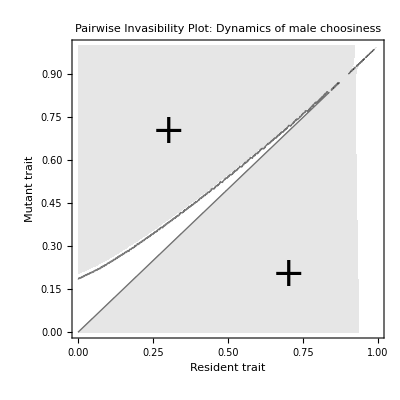

```mathematica
graph1=AddPlus[graph1,0.7,0.2];
graph1=AddPlus[graph1,0.3,0.7];
graph1=Show[graph1, PlotLabel->"Pairwise Invasibility Plot: Dynamics of male choosiness"]
```

```mathematica
TestInvExp[fecond,0,1] (* is not yet defined in the package *)
```

TestInvExp[fecond,0,1]

```mathematica
NFindSP[fecond,0,1] (* is not yet defined in the package *)
```

NFindSP[fecond,0,1]

```mathematica
diff[phip_,phi_]=Re[D[1/(1-s)*g[phi]*dm*s*e*m[phi]/.eq[[1]],phi]]; (* dW(phi,phip)/dphi*)
```

```mathematica
diffLim[phi_]=diff[phi,phi]
```

Re[(0.341053 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))) (0.2525/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))))/((1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi)))) (1+0.189474 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))))^2)-(1.8 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))))/((1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi)))) (1+0.189474 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))))))-(1.8 (0.2525/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))))/((1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi)))) (1+0.189474 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))))))]

```mathematica
diff[0.5,0.5]
```

-17653.8

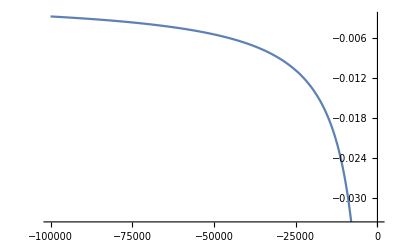

```mathematica
Plot[diffLim[phi],{phi,-100000,1}]
```

```mathematica
Solve[diffLim[phi] == 0, phi]
```

$Aborted

```mathematica
FindRoot[diffLim[phi],{phi,-2000},MaxIterations->10000]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {phi} = {-1.47964×10^163}. Try perturbing the initial point(s).

```mathematica
fecond[0,0.2]
```

6247.65

```mathematica
Limit[diffLim[phi],phi-> -Infinity]
```

0.

```mathematica
diff2[phip_,phi_]=Re[D[1/(1-s)*g[phi]*dm*s*e*m[phi]/.eq[[1]],{phi,2}]]; (* d^2W(phi,phip)/dphi^2*)
```

```mathematica
diff2Lim[phi] = diff2[phi,phi]
```

0.+Re[2.4 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))) (0.+(0.0403878 (0.2525/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))))/((1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))^2 (1+0.189474 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))))^3)-0.213158/((1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))^2 (1+0.189474 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))))^2))-(3.6 ((0.142105 (0.2525/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))))/((1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))) (1+0.189474 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))))^2)-0.75/((1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))) (1+0.189474 (0.25/(1+18/95 (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3)))+(0.75 (1-phi))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+1/(54 2^(2/3) (-1+phi))95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))))))))/(1+18/95 (1-phi) (-(95 (-2+phi))/(54 (-1+phi))-(-18344880+20007000 phi-13358520 phi^2)/(34992 190^(1/3) (-1+phi) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))+(95^(1/3) (-66880+131100 phi+15675 phi^2-43795 phi^3+3 √285 √(-216432-423000 phi-5393804 phi^2+15769630 phi^3-12592841 phi^4+2865600 phi^5-9153 phi^6))^(1/3))/(54 2^(2/3) (-1+phi))))]

```mathematica
Solve[diff2Lim[phi]<0, phi] (* computation too long *)
```

## 2. Dynamics of a system with two hierarchical social classes